```mathematica
Needs["PlotLegends`"]
SetDirectory[NotebookDirectory[]]
pdfs=Partition[Import["pdfs.csv"],27];
pdfs2=Map[Sort[Transpose[{Transpose[#][[1]],Transpose[#][[2]]/Total[Transpose[#][[2]]]}]]&,pdfs];
```

D:\Documents\Projects\Thesis\Analysis

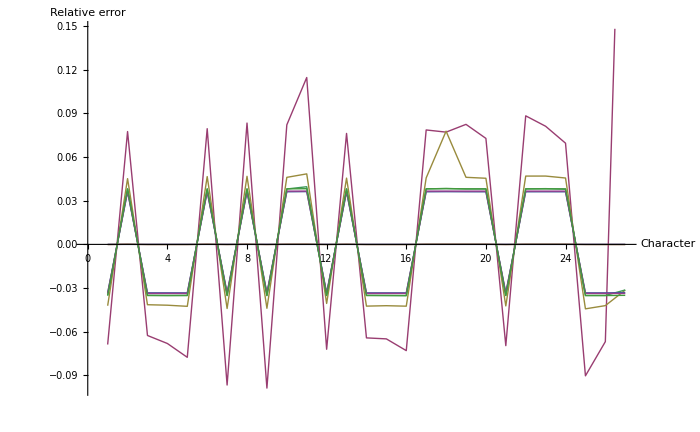

```mathematica
ListPlot[Map[(Transpose[#][[2]]-Transpose[pdfs2[[1]]][[2]])/(Transpose[pdfs2[[1]]][[2]])&,pdfs2],Joined->True,PlotStyle->Thick,ImageSize->700,PlotLegend->{"Original","10^3 bytes","10^4 bytes","10^5 bytes","10^6 bytes","10^7 bytes","Adjusted 10^7","10^6 w/ Adjusted"},LegendSize->{2,0.15},LegendOrientation->Horizontal,AxesLabel->{"Character","Relative error"}]
```